# SyntheticBenchmark

```mathematica
SetOptions[Notebook,"TrackCellChangeTimes"->False,PrivateNotebookOptions->{"FileOutlineCache"->False}];
```

## Flops to Time

```mathematica
modelName="ResNet-50 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

$ModelNames::shdw: Symbol $ModelNames appears in multiple contexts {SyntheticBenchmark`Assets`Models`,Global`}; definitions in context SyntheticBenchmark`Assets`Models` may shadow or be shadowed by other definitions.

```mathematica
flopsToCycles[gpu_,net_?NeuralNetworks`ValidNetQ]:=
flopsToCycles[gpu,FlopCount[net]];
flopsToCycles[gpu_,flops_?AssociationQ]:=
Module[{gpuInfo,latencies,mad,add,div,cmp,exp},
gpuInfo=GPUInformation["TESLA V100 SXM2"];
latencies=gpuInfo["InstructionLatency"];
mad=flops["MultiplyAdds"];
add=flops["Additions"];
div=flops["Divisions"];
cmp=flops["Comparisons"];
exp=flops["Exponentiations"];
mad*latencies["fmad"]+add*latencies["fadd"]+div*latencies["fdiv"]+cmp*latencies["and"]+exp*latencies["lg2"]
]
```

```mathematica
flopsToCycles["TESLA V100 SXM2",lyrs[[1]]]
```

472055808

```mathematica
execTimeOf[gpu_,net_?NeuralNetworks`ValidNetQ]:=
execTimeOf[gpu,flopsToCycles[gpu,net]];
execTimeOf[gpu_,flops_?AssociationQ]:=
execTimeOf[gpu,flopsToCycles[gpu,flops]];
execTimeOf[gpu_,cycles_?NumberQ]:=
N[cycles/GPUInformation[gpu]["ClockRate"]];
```

```mathematica
execTimeOf["TESLA V100 SXM2",lyrs[[1]]]
```

308533.

### get time info for all layers on TESLA V100 SXM2

```mathematica
timeInfo=execTimeOf["TESLA V100 SXM2",#]&/@lyrs;
```

```mathematica
header={"layer name","time"};
Grid[
Prepend[MapThread[Prepend,{List/@Values[timeInfo],Keys[timeInfo]}],header],
Frame->All,
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]
```

layer name | time
{conv1} | 308533.
{bn_conv1} | 107567.
{conv1_relu} | 4197.73
{pool1_pad} | 0.
{pool1} | 4722.45
{2a,res2a_branch1} | 134327.
{2a,bn2a_branch1} | 107567.
{2a,res2a_branch2a} | 33581.8
{2a,bn2a_branch2a} | 26891.7
{2a,res2a_branch2a_relu} | 1049.43
{2a,res2a_branch2b} | 302237.
{2a,bn2a_branch2b} | 26891.7
{2a,res2a_branch2b_relu} | 1049.43
{2a,res2a_branch2c} | 134327.
{2a,bn2a_branch2c} | 107567.
{2a,res2a} | 2098.87
{2a,res2a_relu} | 4197.73
{2b,res2b_branch2a} | 134327.
{2b,bn2b_branch2a} | 26891.7
{2b,res2b_branch2a_relu} | 1049.43
{2b,res2b_branch2b} | 302237.
{2b,bn2b_branch2b} | 26891.7
{2b,res2b_branch2b_relu} | 1049.43
{2b,res2b_branch2c} | 134327.
{2b,bn2b_branch2c} | 107567.
{2b,res2b} | 2098.87
{2b,res2b_relu} | 4197.73
{2c,res2c_branch2a} | 134327.
{2c,bn2c_branch2a} | 26891.7
{2c,res2c_branch2a_relu} | 1049.43
{2c,res2c_branch2b} | 302237.
{2c,bn2c_branch2b} | 26891.7
{2c,res2c_branch2b_relu} | 1049.43
{2c,res2c_branch2c} | 134327.
{2c,bn2c_branch2c} | 107567.
{2c,res2c} | 2098.87
{2c,res2c_relu} | 4197.73
{3a,res3a_branch1} | 268655.
{3a,bn3a_branch1} | 53783.4
{3a,res3a_branch2a} | 67163.7
{3a,bn3a_branch2a} | 13445.9
{3a,res3a_branch2a_relu} | 524.716
{3a,res3a_branch2b} | 302237.
{3a,bn3a_branch2b} | 13445.9
{3a,res3a_branch2b_relu} | 524.716
{3a,res3a_branch2c} | 134327.
{3a,bn3a_branch2c} | 53783.4
{3a,res3a} | 1049.43
{3a,res3a_relu} | 2098.87
{3b,res3b_branch2a} | 134327.
{3b,bn3b_branch2a} | 13445.9
{3b,res3b_branch2a_relu} | 524.716
{3b,res3b_branch2b} | 302237.
{3b,bn3b_branch2b} | 13445.9
{3b,res3b_branch2b_relu} | 524.716
{3b,res3b_branch2c} | 134327.
{3b,bn3b_branch2c} | 53783.4
{3b,res3b} | 1049.43
{3b,res3b_relu} | 2098.87
{3c,res3c_branch2a} | 134327.
{3c,bn3c_branch2a} | 13445.9
{3c,res3c_branch2a_relu} | 524.716
{3c,res3c_branch2b} | 302237.
{3c,bn3c_branch2b} | 13445.9
{3c,res3c_branch2b_relu} | 524.716
{3c,res3c_branch2c} | 134327.
{3c,bn3c_branch2c} | 53783.4
{3c,res3c} | 1049.43
{3c,res3c_relu} | 2098.87
{3d,res3d_branch2a} | 134327.
{3d,bn3d_branch2a} | 13445.9
{3d,res3d_branch2a_relu} | 524.716
{3d,res3d_branch2b} | 302237.
{3d,bn3d_branch2b} | 13445.9
{3d,res3d_branch2b_relu} | 524.716
{3d,res3d_branch2c} | 134327.
{3d,bn3d_branch2c} | 53783.4
{3d,res3d} | 1049.43
{3d,res3d_relu} | 2098.87
{4a,res4a_branch1} | 268655.
{4a,bn4a_branch1} | 26891.7
{4a,res4a_branch2a} | 67163.7
{4a,bn4a_branch2a} | 6722.93
{4a,res4a_branch2a_relu} | 262.358
{4a,res4a_branch2b} | 302237.
{4a,bn4a_branch2b} | 6722.93
{4a,res4a_branch2b_relu} | 262.358
{4a,res4a_branch2c} | 134327.
{4a,bn4a_branch2c} | 26891.7
{4a,res4a} | 524.716
{4a,res4a_relu} | 1049.43
{4b,res4b_branch2a} | 134327.
{4b,bn4b_branch2a} | 6722.93
{4b,res4b_branch2a_relu} | 262.358
{4b,res4b_branch2b} | 302237.
{4b,bn4b_branch2b} | 6722.93
{4b,res4b_branch2b_relu} | 262.358
{4b,res4b_branch2c} | 134327.
{4b,bn4b_branch2c} | 26891.7
{4b,res4b} | 524.716
{4b,res4b_relu} | 1049.43
{4c,res4c_branch2a} | 134327.
{4c,bn4c_branch2a} | 6722.93
{4c,res4c_branch2a_relu} | 262.358
{4c,res4c_branch2b} | 302237.
{4c,bn4c_branch2b} | 6722.93
{4c,res4c_branch2b_relu} | 262.358
{4c,res4c_branch2c} | 134327.
{4c,bn4c_branch2c} | 26891.7
{4c,res4c} | 524.716
{4c,res4c_relu} | 1049.43
{4d,res4d_branch2a} | 134327.
{4d,bn4d_branch2a} | 6722.93
{4d,res4d_branch2a_relu} | 262.358
{4d,res4d_branch2b} | 302237.
{4d,bn4d_branch2b} | 6722.93
{4d,res4d_branch2b_relu} | 262.358
{4d,res4d_branch2c} | 134327.
{4d,bn4d_branch2c} | 26891.7
{4d,res4d} | 524.716
{4d,res4d_relu} | 1049.43
{4e,res4e_branch2a} | 134327.
{4e,bn4e_branch2a} | 6722.93
{4e,res4e_branch2a_relu} | 262.358
{4e,res4e_branch2b} | 302237.
{4e,bn4e_branch2b} | 6722.93
{4e,res4e_branch2b_relu} | 262.358
{4e,res4e_branch2c} | 134327.
{4e,bn4e_branch2c} | 26891.7
{4e,res4e} | 524.716
{4e,res4e_relu} | 1049.43
{4f,res4f_branch2a} | 134327.
{4f,bn4f_branch2a} | 6722.93
{4f,res4f_branch2a_relu} | 262.358
{4f,res4f_branch2b} | 302237.
{4f,bn4f_branch2b} | 6722.93
{4f,res4f_branch2b_relu} | 262.358
{4f,res4f_branch2c} | 134327.
{4f,bn4f_branch2c} | 26891.7
{4f,res4f} | 524.716
{4f,res4f_relu} | 1049.43
{5a,res5a_branch1} | 268655.
{5a,bn5a_branch1} | 13445.9
{5a,res5a_branch2a} | 67163.7
{5a,bn5a_branch2a} | 3361.46
{5a,res5a_branch2a_relu} | 131.179
{5a,res5a_branch2b} | 302237.
{5a,bn5a_branch2b} | 3361.46
{5a,res5a_branch2b_relu} | 131.179
{5a,res5a_branch2c} | 134327.
{5a,bn5a_branch2c} | 13445.9
{5a,res5a} | 262.358
{5a,res5a_relu} | 524.716
{5b,res5b_branch2a} | 134327.
{5b,bn5b_branch2a} | 3361.46
{5b,res5b_branch2a_relu} | 131.179
{5b,res5b_branch2b} | 302237.
{5b,bn5b_branch2b} | 3361.46
{5b,res5b_branch2b_relu} | 131.179
{5b,res5b_branch2c} | 134327.
{5b,bn5b_branch2c} | 13445.9
{5b,res5b} | 262.358
{5b,res5b_relu} | 524.716
{5c,res5c_branch2a} | 134327.
{5c,bn5c_branch2a} | 3361.46
{5c,res5c_branch2a_relu} | 131.179
{5c,res5c_branch2b} | 302237.
{5c,bn5c_branch2b} | 3361.46
{5c,res5c_branch2b_relu} | 131.179
{5c,res5c_branch2c} | 134327.
{5c,bn5c_branch2c} | 13445.9
{5c,res5c} | 262.358
{5c,res5c_relu} | 524.716
{pool5} | 262.358
{flatten_0} | 0.
{fc1000} | 5354.25
{prob} | 154.248

### find Nearest for time on TESLA V100 SXM2

```mathematica
timeInfo=execTimeOf["TESLA V100 SXM2",#]&/@lyrs;
```

```mathematica
nf=Nearest[Values[timeInfo]->Keys[lyrs]]
```

NearestFunction[…]

```mathematica
lyrOfInterest=lyrs[[2]]
```

BatchNormalizationLayer[<>]

```mathematica
nearestLayers=nf[execTimeOf["TESLA V100 SXM2",lyrOfInterest]]
```

{{bn_conv1},{2a,bn2a_branch1},{2a,bn2a_branch2c},{2b,bn2b_branch2c},{2c,bn2c_branch2c}}

```mathematica
Lookup[lyrs,nearestLayers]
```

{BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>]}

## GPU Information

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

```mathematica
GPUMemoryLatency["Volta"]
```

<|l1_cache_access→26,l2_cache_access→198,global_mem_latency→362,local_mem_latency→362,constant_mem_latency→8,texture_mem_latency→436,texture_cache_latency→86,shared_mem_latency→18|>

```mathematica
GPUInstructionLatency["Volta"]
```

<|add→4,sub→4,min→4,max→4,mul→4,mad→4,sdiv→127,srem→125,abs→8,udiv→122,urem→117,and→4,or→4,not→4,xor→4,cnot→8,shl→4,shr→4,fadd→4,fsub→4,fmul→4,fmad→4,fma→4,fdiv→201,dadd→8,dsub→8,dmin→8,dmax→8,dmul→8,dmad→8,dfma→8,ddiv→159,hfadd→6,hfsub→6,hfmul→6,hffma→6,add.cc→4,addc→4,sub.cc→4,subc→8,mad.cc→4,madc→4,rcp→60,sqrt→60,fasqrt→31,rsqrt→31,sin→11,cos→11,lg2→31,ex2→22,copysign→8,mul24→12,mad24→12,mulhi→12,dmulhi→123,sad→4,popc→15,clz→5,bfe→4,bfi→4,bfind→15,bbrev→15,mov→4,shfl→4,cvta→4,cvt→4,selp→4,setp→4|>

```mathematica
GPUInformation["TESLA V100 SXM2"]
```

<|Name→TESLA V100 SXM2,Architecture→Volta,InstructionLatency→<|add→4,sub→4,min→4,max→4,mul→4,mad→4,sdiv→127,srem→125,abs→8,udiv→122,urem→117,and→4,or→4,not→4,xor→4,cnot→8,shl→4,shr→4,fadd→4,fsub→4,fmul→4,fmad→4,fma→4,fdiv→201,dadd→8,dsub→8,dmin→8,dmax→8,dmul→8,dmad→8,dfma→8,ddiv→159,hfadd→6,hfsub→6,hfmul→6,hffma→6,add.cc→4,addc→4,sub.cc→4,subc→8,mad.cc→4,madc→4,rcp→60,sqrt→60,fasqrt→31,rsqrt→31,sin→11,cos→11,lg2→31,ex2→22,copysign→8,mul24→12,mad24→12,mulhi→12,dmulhi→123,sad→4,popc→15,clz→5,bfe→4,bfi→4,bfind→15,bbrev→15,mov→4,shfl→4,cvta→4,cvt→4,selp→4,setp→4|>,MemoryLatency→<|l1_cache_access→26,l2_cache_access→198,global_mem_latency→362,local_mem_latency→362,constant_mem_latency→8,texture_mem_latency→436,texture_cache_latency→86,shared_mem_latency→18|>,Interconnect→<|Name→SXM2,Bandwidth→Missing[SXM2,Not implemented]|>,ClockRate→1530,PeekGFlops→15000,MemoryBandwidth→900|>

## Flop Count

```mathematica
modelName="ResNet-50 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

### get flop info for all layers

```mathematica
flopsInfo=FlopCount/@lyrs;
```

```mathematica
header=Prepend[Keys[flopsInfo[[1]]],"layer name"];
Grid[
Prepend[MapThread[Prepend,{Values/@Values[flopsInfo],Keys[flopsInfo]}],header],
Frame->All,
Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}
]
```

layer name | MultiplyAdds | Additions | Divisions | Comparisons | Exponentiations
{conv1} | 118013952 | 0 | 0 | 0 | 0
{bn_conv1} | 0 | 802816 | 802816 | 0 | 0
{conv1_relu} | 802816 | 0 | 0 | 802816 | 0
{pool1_pad} | 0 | 0 | 0 | 0 | 0
{pool1} | 0 | 0 | 0 | 1806336 | 0
{2a,res2a_branch1} | 51380224 | 0 | 0 | 0 | 0
{2a,bn2a_branch1} | 0 | 802816 | 802816 | 0 | 0
{2a,res2a_branch2a} | 12845056 | 0 | 0 | 0 | 0
{2a,bn2a_branch2a} | 0 | 200704 | 200704 | 0 | 0
{2a,res2a_branch2a_relu} | 200704 | 0 | 0 | 200704 | 0
{2a,res2a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{2a,bn2a_branch2b} | 0 | 200704 | 200704 | 0 | 0
{2a,res2a_branch2b_relu} | 200704 | 0 | 0 | 200704 | 0
{2a,res2a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{2a,bn2a_branch2c} | 0 | 802816 | 802816 | 0 | 0
{2a,res2a} | 0 | 802816 | 0 | 0 | 0
{2a,res2a_relu} | 802816 | 0 | 0 | 802816 | 0
{2b,res2b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{2b,bn2b_branch2a} | 0 | 200704 | 200704 | 0 | 0
{2b,res2b_branch2a_relu} | 200704 | 0 | 0 | 200704 | 0
{2b,res2b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{2b,bn2b_branch2b} | 0 | 200704 | 200704 | 0 | 0
{2b,res2b_branch2b_relu} | 200704 | 0 | 0 | 200704 | 0
{2b,res2b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{2b,bn2b_branch2c} | 0 | 802816 | 802816 | 0 | 0
{2b,res2b} | 0 | 802816 | 0 | 0 | 0
{2b,res2b_relu} | 802816 | 0 | 0 | 802816 | 0
{2c,res2c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{2c,bn2c_branch2a} | 0 | 200704 | 200704 | 0 | 0
{2c,res2c_branch2a_relu} | 200704 | 0 | 0 | 200704 | 0
{2c,res2c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{2c,bn2c_branch2b} | 0 | 200704 | 200704 | 0 | 0
{2c,res2c_branch2b_relu} | 200704 | 0 | 0 | 200704 | 0
{2c,res2c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{2c,bn2c_branch2c} | 0 | 802816 | 802816 | 0 | 0
{2c,res2c} | 0 | 802816 | 0 | 0 | 0
{2c,res2c_relu} | 802816 | 0 | 0 | 802816 | 0
{3a,res3a_branch1} | 102760448 | 0 | 0 | 0 | 0
{3a,bn3a_branch1} | 0 | 401408 | 401408 | 0 | 0
{3a,res3a_branch2a} | 25690112 | 0 | 0 | 0 | 0
{3a,bn3a_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3a,res3a_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3a,res3a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3a,bn3a_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3a,res3a_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3a,res3a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3a,bn3a_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3a,res3a} | 0 | 401408 | 0 | 0 | 0
{3a,res3a_relu} | 401408 | 0 | 0 | 401408 | 0
{3b,res3b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{3b,bn3b_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3b,res3b_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3b,res3b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3b,bn3b_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3b,res3b_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3b,res3b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3b,bn3b_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3b,res3b} | 0 | 401408 | 0 | 0 | 0
{3b,res3b_relu} | 401408 | 0 | 0 | 401408 | 0
{3c,res3c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{3c,bn3c_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3c,res3c_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3c,res3c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3c,bn3c_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3c,res3c_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3c,res3c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3c,bn3c_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3c,res3c} | 0 | 401408 | 0 | 0 | 0
{3c,res3c_relu} | 401408 | 0 | 0 | 401408 | 0
{3d,res3d_branch2a} | 51380224 | 0 | 0 | 0 | 0
{3d,bn3d_branch2a} | 0 | 100352 | 100352 | 0 | 0
{3d,res3d_branch2a_relu} | 100352 | 0 | 0 | 100352 | 0
{3d,res3d_branch2b} | 115605504 | 0 | 0 | 0 | 0
{3d,bn3d_branch2b} | 0 | 100352 | 100352 | 0 | 0
{3d,res3d_branch2b_relu} | 100352 | 0 | 0 | 100352 | 0
{3d,res3d_branch2c} | 51380224 | 0 | 0 | 0 | 0
{3d,bn3d_branch2c} | 0 | 401408 | 401408 | 0 | 0
{3d,res3d} | 0 | 401408 | 0 | 0 | 0
{3d,res3d_relu} | 401408 | 0 | 0 | 401408 | 0
{4a,res4a_branch1} | 102760448 | 0 | 0 | 0 | 0
{4a,bn4a_branch1} | 0 | 200704 | 200704 | 0 | 0
{4a,res4a_branch2a} | 25690112 | 0 | 0 | 0 | 0
{4a,bn4a_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4a,res4a_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4a,res4a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4a,bn4a_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4a,res4a_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4a,res4a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4a,bn4a_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4a,res4a} | 0 | 200704 | 0 | 0 | 0
{4a,res4a_relu} | 200704 | 0 | 0 | 200704 | 0
{4b,res4b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4b,bn4b_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4b,res4b_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4b,res4b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4b,bn4b_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4b,res4b_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4b,res4b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4b,bn4b_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4b,res4b} | 0 | 200704 | 0 | 0 | 0
{4b,res4b_relu} | 200704 | 0 | 0 | 200704 | 0
{4c,res4c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4c,bn4c_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4c,res4c_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4c,res4c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4c,bn4c_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4c,res4c_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4c,res4c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4c,bn4c_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4c,res4c} | 0 | 200704 | 0 | 0 | 0
{4c,res4c_relu} | 200704 | 0 | 0 | 200704 | 0
{4d,res4d_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4d,bn4d_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4d,res4d_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4d,res4d_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4d,bn4d_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4d,res4d_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4d,res4d_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4d,bn4d_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4d,res4d} | 0 | 200704 | 0 | 0 | 0
{4d,res4d_relu} | 200704 | 0 | 0 | 200704 | 0
{4e,res4e_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4e,bn4e_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4e,res4e_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4e,res4e_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4e,bn4e_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4e,res4e_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4e,res4e_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4e,bn4e_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4e,res4e} | 0 | 200704 | 0 | 0 | 0
{4e,res4e_relu} | 200704 | 0 | 0 | 200704 | 0
{4f,res4f_branch2a} | 51380224 | 0 | 0 | 0 | 0
{4f,bn4f_branch2a} | 0 | 50176 | 50176 | 0 | 0
{4f,res4f_branch2a_relu} | 50176 | 0 | 0 | 50176 | 0
{4f,res4f_branch2b} | 115605504 | 0 | 0 | 0 | 0
{4f,bn4f_branch2b} | 0 | 50176 | 50176 | 0 | 0
{4f,res4f_branch2b_relu} | 50176 | 0 | 0 | 50176 | 0
{4f,res4f_branch2c} | 51380224 | 0 | 0 | 0 | 0
{4f,bn4f_branch2c} | 0 | 200704 | 200704 | 0 | 0
{4f,res4f} | 0 | 200704 | 0 | 0 | 0
{4f,res4f_relu} | 200704 | 0 | 0 | 200704 | 0
{5a,res5a_branch1} | 102760448 | 0 | 0 | 0 | 0
{5a,bn5a_branch1} | 0 | 100352 | 100352 | 0 | 0
{5a,res5a_branch2a} | 25690112 | 0 | 0 | 0 | 0
{5a,bn5a_branch2a} | 0 | 25088 | 25088 | 0 | 0
{5a,res5a_branch2a_relu} | 25088 | 0 | 0 | 25088 | 0
{5a,res5a_branch2b} | 115605504 | 0 | 0 | 0 | 0
{5a,bn5a_branch2b} | 0 | 25088 | 25088 | 0 | 0
{5a,res5a_branch2b_relu} | 25088 | 0 | 0 | 25088 | 0
{5a,res5a_branch2c} | 51380224 | 0 | 0 | 0 | 0
{5a,bn5a_branch2c} | 0 | 100352 | 100352 | 0 | 0
{5a,res5a} | 0 | 100352 | 0 | 0 | 0
{5a,res5a_relu} | 100352 | 0 | 0 | 100352 | 0
{5b,res5b_branch2a} | 51380224 | 0 | 0 | 0 | 0
{5b,bn5b_branch2a} | 0 | 25088 | 25088 | 0 | 0
{5b,res5b_branch2a_relu} | 25088 | 0 | 0 | 25088 | 0
{5b,res5b_branch2b} | 115605504 | 0 | 0 | 0 | 0
{5b,bn5b_branch2b} | 0 | 25088 | 25088 | 0 | 0
{5b,res5b_branch2b_relu} | 25088 | 0 | 0 | 25088 | 0
{5b,res5b_branch2c} | 51380224 | 0 | 0 | 0 | 0
{5b,bn5b_branch2c} | 0 | 100352 | 100352 | 0 | 0
{5b,res5b} | 0 | 100352 | 0 | 0 | 0
{5b,res5b_relu} | 100352 | 0 | 0 | 100352 | 0
{5c,res5c_branch2a} | 51380224 | 0 | 0 | 0 | 0
{5c,bn5c_branch2a} | 0 | 25088 | 25088 | 0 | 0
{5c,res5c_branch2a_relu} | 25088 | 0 | 0 | 25088 | 0
{5c,res5c_branch2b} | 115605504 | 0 | 0 | 0 | 0
{5c,bn5c_branch2b} | 0 | 25088 | 25088 | 0 | 0
{5c,res5c_branch2b_relu} | 25088 | 0 | 0 | 25088 | 0
{5c,res5c_branch2c} | 51380224 | 0 | 0 | 0 | 0
{5c,bn5c_branch2c} | 0 | 100352 | 100352 | 0 | 0
{5c,res5c} | 0 | 100352 | 0 | 0 | 0
{5c,res5c_relu} | 100352 | 0 | 0 | 100352 | 0
{pool5} | 0 | 100352 | 0 | 0 | 0
{flatten_0} | 0 | 0 | 0 | 0 | 0
{fc1000} | 2048000 | 0 | 0 | 0 | 0
{prob} | 0 | 1000 | 1000 | 0 | 1000

### find Nearest for flops

```mathematica
flopsInfo=FlopCount/@lyrs;
```

```mathematica
nf=Nearest[(Values/@Values[flopsInfo])->Keys[lyrs]]
```

NearestFunction[…]

```mathematica
lyrOfInterest=lyrs[[2]]
```

BatchNormalizationLayer[<>]

```mathematica
nearestLayers=nf[Values[FlopCount[lyrOfInterest]]]
```

{{bn_conv1},{2a,bn2a_branch1},{2a,bn2a_branch2c},{2b,bn2b_branch2c},{2c,bn2c_branch2c}}

```mathematica
Lookup[lyrs,nearestLayers]
```

{BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>],BatchNormalizationLayer[<>]}

### All Models

```mathematica
PrependTo[$Path,FileNameJoin[{NotebookDirectory[]}]];
<<SyntheticBenchmark`
<<SyntheticBenchmark`StaticAnalysis`
```

$Models::shdw: Symbol $Models appears in multiple contexts {SyntheticBenchmark`Assets`Models`,Global`}; definitions in context SyntheticBenchmark`Assets`Models` may shadow or be shadowed by other definitions.

```mathematica
modelTask=GroupBy[Table[model->If[NetModel[ model,"TaskType"]==={},"Other",First[NetModel[ model,"TaskType"]]],{model,Keys[$Models]}]];models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
taskName="Classification";
```

```mathematica
lyrs=Union[Flatten[Lookup[$Models,models[taskName]]]];
```

```mathematica
<<SyntheticBenchmark`StaticAnalysis`
es=RandomSample[lyrs];
Select[Check[FlopCount[#],Throw[#]]&/@es,!AssociationQ[#]&]
```

{}

```mathematica
es//FullForm
```

Function["ScaledExponentialLinearUnit"[Slot[1]]]

unhandled ElementwiseLayer case<|Function→NeuralNetworks`ValidatedParameter[NeuralNetworks`Private`ScalarFunctionObject[-Graphics-]],$Dimensions→{816,7,7}|>

Part::partw: Part 2 of {50} does not exist.

unhandled ElementwiseLayer case<|Function→NeuralNetworks`ValidatedParameter[NeuralNetworks`Private`ScalarFunctionObject[-Graphics-]],$Dimensions→{288,28,28}|>

{Null,Null,Null,Null,Null,Null}

## Layer Patterns

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
layerNameKinds=Flatten[Table[
model=NetModel[modelName];
gr=NetInformation[model,"LayersGraph"];
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
layers=SymbolName/@layers[[All,0]];
Append[layers,"NONE"],
{modelName,$ModelNames}
]];
```

$Aborted

```mathematica
shortenName[s_String]:=StringReplace[s,{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}];
shortenName[s_?Developer`SymbolQ]:=shortenName[SymbolName[s]]
```

```mathematica
mkChart[n_]:=Module[{tuples,stuples},
tuples=Association[Counts[Partition[layerNameKinds,n,1]]];
stuples=Take[ReverseSort[KeyMap[StringRiffle[Map[shortenName,#],"⟩"]&,tuples]],UpTo[10]];
BarChart[
stuples,
ChartLabels->Map[Rotate[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[stuples]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
]
```

### Size 2 patterns

```mathematica
mkChart[2]
```

Table::iterb: Iterator {modelName,$ModelNames} does not have appropriate bounds.

Counts::invl: The argument Table[model=NetModel[modelName];gr=NetInformation[model,LayersGraph];topo=TopologicalSort[gr];layers=Lookup[NetInformation[model,Layers],topo];layers=SymbolName/@layers⟦All,0⟧;Append[layers,NONE],{modelName,$ModelNames}] is not a list.

KeyMap::invak: The argument Association[Counts[Partition[layerNameKinds,2,1]]] is not a valid Association.

Keys::invrl: The argument KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,2,1]]]] is not a valid Association or a list of rules.

BarChart::ldata: KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,2,1]]]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,2,1]]]],ChartLabels→Keys[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,2,1]]]]],ChartStyle→{GrayLevel[0]},PlotTheme→Grid,AspectRatio→1/6,Frame→True,ImageSize→Scaled[0.75],FrameStyle→Directive[AbsoluteThickness[0.5],GrayLevel[0]],BaseStyle→{FontFamily→Latin Modern Roman,FontColor→GrayLevel[0],FontSize→10}]

### Size 3 patterns

```mathematica
mkChart[3]
```

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Counts::invl: The argument Table[] is not a list.

KeyMap::invak: The argument Association[Counts[Partition[layerNameKinds,3,1]]] is not a valid Association.

Keys::invrl: The argument KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,3,1]]]] is not a valid Association or a list of rules.

BarChart::ldata: KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,3,1]]]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,3,1]]]],ChartLabels→Keys[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,3,1]]]]],ChartStyle→{GrayLevel[0]},PlotTheme→Grid,AspectRatio→1/6,Frame→True,ImageSize→Scaled[0.75],FrameStyle→Directive[AbsoluteThickness[0.5],GrayLevel[0]],BaseStyle→{FontFamily→Latin Modern Roman,FontColor→GrayLevel[0],FontSize→10}]

### Size 4 patterns

```mathematica
mkChart[4]
```

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Counts::invl: The argument Table[] is not a list.

KeyMap::invak: The argument Association[Counts[Partition[layerNameKinds,4,1]]] is not a valid Association.

Keys::invrl: The argument KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,4,1]]]] is not a valid Association or a list of rules.

BarChart::ldata: KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,4,1]]]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,4,1]]]],ChartLabels→Keys[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,4,1]]]]],ChartStyle→{GrayLevel[0]},PlotTheme→Grid,AspectRatio→1/6,Frame→True,ImageSize→Scaled[0.75],FrameStyle→Directive[AbsoluteThickness[0.5],GrayLevel[0]],BaseStyle→{FontFamily→Latin Modern Roman,FontColor→GrayLevel[0],FontSize→10}]

### Size 5 patterns

```mathematica
mkChart[5]
```

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Counts::invl: The argument Table[] is not a list.

KeyMap::invak: The argument Association[Counts[Partition[layerNameKinds,5,1]]] is not a valid Association.

Keys::invrl: The argument KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,5,1]]]] is not a valid Association or a list of rules.

BarChart::ldata: KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,5,1]]]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,5,1]]]],ChartLabels→Keys[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,5,1]]]]],ChartStyle→{GrayLevel[0]},PlotTheme→Grid,AspectRatio→1/6,Frame→True,ImageSize→Scaled[0.75],FrameStyle→Directive[AbsoluteThickness[0.5],GrayLevel[0]],BaseStyle→{FontFamily→Latin Modern Roman,FontColor→GrayLevel[0],FontSize→10}]

### Size 6 patterns

```mathematica
mkChart[6]
```

Table::argm: Table called with 0 arguments; 1 or more arguments are expected.

Counts::invl: The argument Table[] is not a list.

KeyMap::invak: The argument Association[Counts[Partition[layerNameKinds,6,1]]] is not a valid Association.

Keys::invrl: The argument KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,6,1]]]] is not a valid Association or a list of rules.

BarChart::ldata: KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,6,1]]]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,6,1]]]],ChartLabels→Keys[KeyMap[StringRiffle[shortenName/@#1,⟩]&,Association[Counts[Partition[layerNameKinds,6,1]]]]],ChartStyle→{GrayLevel[0]},PlotTheme→Grid,AspectRatio→1/6,Frame→True,ImageSize→Scaled[0.75],FrameStyle→Directive[AbsoluteThickness[0.5],GrayLevel[0]],BaseStyle→{FontFamily→Latin Modern Roman,FontColor→GrayLevel[0],FontSize→10}]

## NetInformation Metadata

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
$ModelNames[[20]]
```

CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data

```mathematica
model=NetModel[$ModelNames[[20]]];
```

```mathematica
NetInformation[model,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

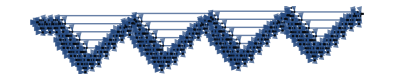

```mathematica
gr=NetInformation[model,"LayersGraph"]
```

### Mc

https://blog.wolfram.com/2013/02/04/centennial-of-markov-chains/

```mathematica
Frequencies[data_]:=Block[{ta=Tally[data]},ta[[All,2]]/=N[Length[data]];Rule@@@ta]
```

```mathematica
gr=NetInformation[model,"LayersGraph"];
verts=VertexList[gr];
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
```

```mathematica
layerNameKinds=Flatten[Parallelize@Table[
model=NetModel[modelName];
gr=NetInformation[model,"LayersGraph"];
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
layers=SymbolName/@layers[[All,0]];
Append[layers,"NONE"],
{modelName,$ModelNames}
]];
fverts=Frequencies[layerNameKinds];
fvertTup=Frequencies[Partition[layerNameKinds,2,1]];
```

```mathematica
Length[layerNameKinds]
```

91

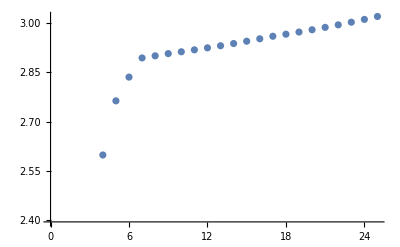

```mathematica
Table[{k,Entropy[Partition[layerNameKinds,k,1]]//N},{k,1,25}]//ListPlot
```

```mathematica
condprobs=Catenate@Table[
Frequencies[Cases[Partition[layerNameKinds,2,1],{lyr,_}]],{lyr,layerNameKinds}];
```

```mathematica
MatrixForm[tm=Outer[List,Union[layerNameKinds],Union[layerNameKinds]]/.Append[condprobs,{_,_}->0]]
```

(0 | 0 | 0.0454545 | 0.954545 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0
0.133333 | 0.0666667 | 0 | 0 | 0.8 | 0 | 0
0 | 0 | 0.608696 | 0 | 0 | 0 | 0.391304
1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0.111111 | 0 | 0 | 0.888889 | 0 | 0)

```mathematica
mproc=DiscreteMarkovProcess[1,tm]
```

DiscreteMarkovProcess[1,{{0,0,0.0454545,0.954545,0,0,0},{0,0,0,0,0,1.,0},{0.133333,0.0666667,0,0,0.8,0,0},{0,0,0.608696,0,0,0,0.391304},{1.,0,0,0,0,0,0},{0,0,0,1.,0,0,0},{0,0.111111,0,0,0.888889,0,0}}]

```mathematica
Mean[FirstPassageTimeDistribution[mproc,1]]
```

4.22727

```mathematica
DiscretePlot[PDF[FirstPassageTimeDistribution[mproc,1],n],{n,1,10},ExtentSize->{0,2/3},PlotStyle->Black]
```

-Graphics-

```mathematica
(gram4data=Flatten[Frequencies/@GatherBy[Partition[layerNameKinds,4,1],Most]]//N)//Short[#,3]&
```

{{ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer}→0.916667,«18»,{ElementwiseLayer,DeconvolutionLayer,PartLayer,NormalizationLayer}→1.}

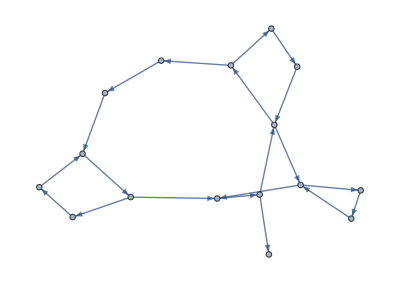

```mathematica
gram4gr=Graph[gram4data/.{HoldPattern[{w1_,w2_,w3_,w4_}->p_]:>Property[{w1,w2,w3}->{w2,w3,w4},"Probability"->p]},PerformanceGoal->"Speed"]
```

```mathematica
initialProbabilityVector=SparseArray[VertexList[gram4gr]/.Frequencies[Partition[layerNameKinds,3,1]]];
```

```mathematica
transitionMat=WeightedAdjacencyMatrix[gram4gr,EdgeWeight->"Probability"]
```

SparseArray[…]

```mathematica
mc=DiscreteMarkovProcess[initialProbabilityVector//N,transitionMat]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

DiscreteMarkovProcess[{0.130435,0.206522,0.0108696,0.130435,0.0978261,0.0217391,0.119565,0.0217391,0.0869565,0.0108696,0.0869565,0.0108696,0.0217391,0.0217391,0.0108696,0.0108696},{{0.,0.916667,0.0833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.526316,0.473684,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.166667,0.833333,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.888889,0.111111,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.5,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.}}]

```mathematica
GramListToText[list_]:=StringJoin[Riffle[Join[First[list],Rest[list][[All,-1]]]," "]]
```

```mathematica
GramListToText[Extract[VertexList[gram4gr],Transpose[RandomFunction[mc,{0,100}]["States"]]]]
```

ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer TotalLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer DeconvolutionLayer PartLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer NormalizationLayer ElementwiseLayer PaddingLayer ConvolutionLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer ElementwiseLayer

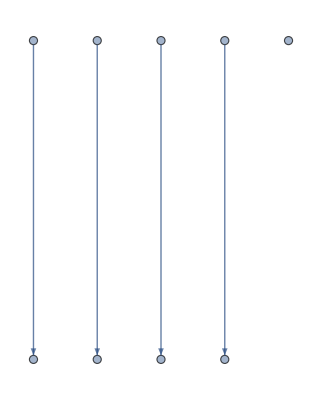

```mathematica
lines=VertexDelete[gram4gr,VertexList[gram4gr, x_/;VertexDegree[gram4gr,x]>2]]
```

```mathematica
lineData=WeaklyConnectedComponents[lines];
```

### topological order

```mathematica
topo=TopologicalSort[gr];
layers=Lookup[NetInformation[model,"Layers"],topo];
layerNameKinds=layers[[All,0]]
```

{ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,NormalizationLayer,TotalLayer,DeconvolutionLayer,PartLayer,NormalizationLayer,ElementwiseLayer,DeconvolutionLayer,PartLayer,NormalizationLayer,ElementwiseLayer,PaddingLayer,ConvolutionLayer,ElementwiseLayer}

```mathematica
verts=VertexList[gr];
edges=EdgeList[gr];
```

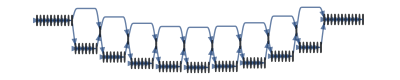

```mathematica
gre=Graph[verts,edges,Options[gr],AnnotationRules->Join[
Table[vert->{"InitialProbability"->1/Length[verts]},{vert,verts}],
Table[edge->{"Probability"->1},{edge,edges}]
]]
```

```mathematica
de=DiscreteMarkovProcess[gre];
```

```mathematica
tmp=RandomFunction[de,{0,10}]
```

TemporalData[…]

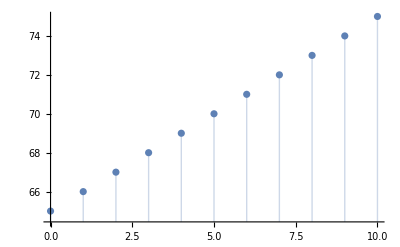

```mathematica
ListPlot[tmp,Filling->Axis]
```

```mathematica
sim=RandomFunction[de,{0,10},4*10,Method->{Automatic,"StoppingFunction"->Function[{len,pos},len<10&&pos≠1||len==1]}]
```

TemporalData[…]

```mathematica
Normal[sim]
```

{{{0,72},{1,73},{2,74},{3,75},{4,76},{5,77},{6,78},{7,79},{8,80},{9,81}},{{0,66},{1,67},{2,68},{3,69},{4,70},{5,71},{6,72},{7,73},{8,74},{9,75}},{{0,15},{1,16},{2,17},{3,18},{4,19},{5,20},{6,21},{7,22},{8,23},{9,24}},{{0,81},{1,82},{2,83},{3,84},{4,85},{5,86},{6,87},{7,88},{8,89},{9,90}},{{0,51},{1,52},{2,53},{3,54},{4,55},{5,56},{6,57},{7,58},{8,59},{9,67}},{{0,51},{1,59},{2,67},{3,68},{4,69},{5,70},{6,71},{7,72},{8,73},{9,74}},{{0,35},{1,43},{2,51},{3,52},{4,53},{5,54},{6,55},{7,56},{8,57},{9,58}},{{0,3},{1,4},{2,5},{3,6},{4,7},{5,8},{6,9},{7,10},{8,11},{9,12}},{{0,66},{1,67},{2,75},{3,83},{4,84},{5,85},{6,86},{7,87},{8,88},{9,89}},{{0,79},{1,80},{2,81},{3,82},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,70},{1,71},{2,72},{3,73},{4,74},{5,75},{6,76},{7,77},{8,78},{9,79}},{{0,41},{1,42},{2,43},{3,44},{4,45},{5,46},{6,47},{7,48},{8,49},{9,50}},{{0,18},{1,19},{2,27},{3,28},{4,29},{5,30},{6,31},{7,32},{8,33},{9,34}},{{0,58},{1,59},{2,67},{3,75},{4,76},{5,77},{6,78},{7,79},{8,80},{9,81}},{{0,78},{1,79},{2,80},{3,81},{4,82},{5,83},{6,84},{7,85},{8,86},{9,87}},{{0,79},{1,80},{2,81},{3,82},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,75},{1,83},{2,84},{3,85},{4,86},{5,87},{6,88},{7,89},{8,90},{9,91}},{{0,5},{1,6},{2,7},{3,8},{4,9},{5,10},{6,11},{7,12},{8,13},{9,14}},{{0,53},{1,54},{2,55},{3,56},{4,57},{5,58},{6,59},{7,67},{8,75},{9,83}},{{0,58},{1,59},{2,67},{3,75},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,37},{1,38},{2,39},{3,40},{4,41},{5,42},{6,43},{7,44},{8,45},{9,46}},{{0,86},{1,87},{2,88},{3,89},{4,90},{5,91},{6,92},{7,93},{8,94},{9,94}},{{0,40},{1,41},{2,42},{3,43},{4,44},{5,45},{6,46},{7,47},{8,48},{9,49}},{{0,75},{1,83},{2,84},{3,85},{4,86},{5,87},{6,88},{7,89},{8,90},{9,91}},{{0,55},{1,56},{2,57},{3,58},{4,59},{5,67},{6,68},{7,69},{8,70},{9,71}},{{0,60},{1,61},{2,62},{3,63},{4,64},{5,65},{6,66},{7,67},{8,75},{9,83}},{{0,75},{1,76},{2,77},{3,78},{4,79},{5,80},{6,81},{7,82},{8,83},{9,84}},{{0,88},{1,89},{2,90},{3,91},{4,92},{5,93},{6,94},{7,94},{8,94},{9,94}},{{0,62},{1,63},{2,64},{3,65},{4,66},{5,67},{6,75},{7,83},{8,84},{9,85}},{{0,26},{1,27},{2,28},{3,29},{4,30},{5,31},{6,32},{7,33},{8,34},{9,35}},{{0,46},{1,47},{2,48},{3,49},{4,50},{5,51},{6,59},{7,67},{8,75},{9,83}},{{0,25},{1,26},{2,27},{3,35},{4,43},{5,44},{6,45},{7,46},{8,47},{9,48}},{{0,8},{1,9},{2,10},{3,11},{4,12},{5,13},{6,14},{7,15},{8,16},{9,17}},{{0,89},{1,90},{2,91},{3,92},{4,93},{5,94},{6,94},{7,94},{8,94},{9,94}},{{0,15},{1,16},{2,17},{3,18},{4,19},{5,27},{6,28},{7,29},{8,30},{9,31}},{{0,39},{1,40},{2,41},{3,42},{4,43},{5,51},{6,52},{7,53},{8,54},{9,55}},{{0,52},{1,53},{2,54},{3,55},{4,56},{5,57},{6,58},{7,59},{8,67},{9,75}},{{0,79},{1,80},{2,81},{3,82},{4,83},{5,84},{6,85},{7,86},{8,87},{9,88}},{{0,81},{1,82},{2,83},{3,84},{4,85},{5,86},{6,87},{7,88},{8,89},{9,90}},{{0,19},{1,27},{2,35},{3,36},{4,37},{5,38},{6,39},{7,40},{8,41},{9,42}}}

### mxnet graph

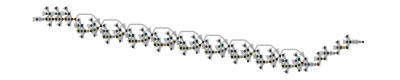

```mathematica
mr=NetInformation[model,"MXNetNodeGraph"]
```

### play with graph

```mathematica
gr=NetInformation[model,"LayersGraph"]
```

-Graphics-

```mathematica
VertexList[gr]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12,1,1},{12,1,2},{12,1,3},{12,1,4},{12,1,5},{12,1,6},{12,1,7},{12,2},{13,1,1},{13,1,2},{13,1,3},{13,1,4},{13,1,5},{13,1,6},{13,1,7},{13,2},{14,1,1},{14,1,2},{14,1,3},{14,1,4},{14,1,5},{14,1,6},{14,1,7},{14,2},{15,1,1},{15,1,2},{15,1,3},{15,1,4},{15,1,5},{15,1,6},{15,1,7},{15,2},{16,1,1},{16,1,2},{16,1,3},{16,1,4},{16,1,5},{16,1,6},{16,1,7},{16,2},{17,1,1},{17,1,2},{17,1,3},{17,1,4},{17,1,5},{17,1,6},{17,1,7},{17,2},{18,1,1},{18,1,2},{18,1,3},{18,1,4},{18,1,5},{18,1,6},{18,1,7},{18,2},{19,1,1},{19,1,2},{19,1,3},{19,1,4},{19,1,5},{19,1,6},{19,1,7},{19,2},{20,1,1},{20,1,2},{20,1,3},{20,1,4},{20,1,5},{20,1,6},{20,1,7},{20,2},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31}}

```mathematica
ConnectedComponents[gr]
```

{{{31}},{{30}},{{29}},{{28}},{{27}},{{26}},{{25}},{{24}},{{23}},{{22}},{{21}},{{20,2}},{{20,1,7}},{{20,1,6}},{{20,1,5}},{{20,1,4}},{{20,1,3}},{{20,1,2}},{{20,1,1}},{{19,2}},{{19,1,7}},{{19,1,6}},{{19,1,5}},{{19,1,4}},{{19,1,3}},{{19,1,2}},{{19,1,1}},{{18,2}},{{18,1,7}},{{18,1,6}},{{18,1,5}},{{18,1,4}},{{18,1,3}},{{18,1,2}},{{18,1,1}},{{17,2}},{{17,1,7}},{{17,1,6}},{{17,1,5}},{{17,1,4}},{{17,1,3}},{{17,1,2}},{{17,1,1}},{{16,2}},{{16,1,7}},{{16,1,6}},{{16,1,5}},{{16,1,4}},{{16,1,3}},{{16,1,2}},{{16,1,1}},{{15,2}},{{15,1,7}},{{15,1,6}},{{15,1,5}},{{15,1,4}},{{15,1,3}},{{15,1,2}},{{15,1,1}},{{14,2}},{{14,1,7}},{{14,1,6}},{{14,1,5}},{{14,1,4}},{{14,1,3}},{{14,1,2}},{{14,1,1}},{{13,2}},{{13,1,7}},{{13,1,6}},{{13,1,5}},{{13,1,4}},{{13,1,3}},{{13,1,2}},{{13,1,1}},{{12,2}},{{12,1,7}},{{12,1,6}},{{12,1,5}},{{12,1,4}},{{12,1,3}},{{12,1,2}},{{12,1,1}},{{11}},{{10}},{{9}},{{8}},{{7}},{{6}},{{5}},{{4}},{{3}},{{2}},{{1}}}

```mathematica
components=ConnectedComponents[gr]
```

{{{31}},{{30}},{{29}},{{28}},{{27}},{{26}},{{25}},{{24}},{{23}},{{22}},{{21}},{{20,2}},{{20,1,7}},{{20,1,6}},{{20,1,5}},{{20,1,4}},{{20,1,3}},{{20,1,2}},{{20,1,1}},{{19,2}},{{19,1,7}},{{19,1,6}},{{19,1,5}},{{19,1,4}},{{19,1,3}},{{19,1,2}},{{19,1,1}},{{18,2}},{{18,1,7}},{{18,1,6}},{{18,1,5}},{{18,1,4}},{{18,1,3}},{{18,1,2}},{{18,1,1}},{{17,2}},{{17,1,7}},{{17,1,6}},{{17,1,5}},{{17,1,4}},{{17,1,3}},{{17,1,2}},{{17,1,1}},{{16,2}},{{16,1,7}},{{16,1,6}},{{16,1,5}},{{16,1,4}},{{16,1,3}},{{16,1,2}},{{16,1,1}},{{15,2}},{{15,1,7}},{{15,1,6}},{{15,1,5}},{{15,1,4}},{{15,1,3}},{{15,1,2}},{{15,1,1}},{{14,2}},{{14,1,7}},{{14,1,6}},{{14,1,5}},{{14,1,4}},{{14,1,3}},{{14,1,2}},{{14,1,1}},{{13,2}},{{13,1,7}},{{13,1,6}},{{13,1,5}},{{13,1,4}},{{13,1,3}},{{13,1,2}},{{13,1,1}},{{12,2}},{{12,1,7}},{{12,1,6}},{{12,1,5}},{{12,1,4}},{{12,1,3}},{{12,1,2}},{{12,1,1}},{{11}},{{10}},{{9}},{{8}},{{7}},{{6}},{{5}},{{4}},{{3}},{{2}},{{1}}}

Construct the condensation of g by finding the edges between the components:

```mathematica
edges=Union[Cases[EdgeList[gr]/.Table[v->First[Select[components,MemberQ[#,v]&]],{v,VertexList[gr]}],u_->v_/;u=!=v]];
```

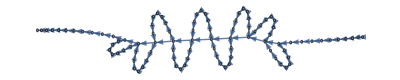

```mathematica
cond=Graph[components,edges]
```

Use the topological ordering of the strongly connected components to order the vertices of g:

```mathematica
tp=TopologicalSort[cond]
```

{{{1}},{{2}},{{3}},{{4}},{{5}},{{6}},{{7}},{{8}},{{9}},{{10}},{{11}},{{12,1,1}},{{12,1,2}},{{12,1,3}},{{12,1,4}},{{12,1,5}},{{12,1,6}},{{12,1,7}},{{12,2}},{{13,1,1}},{{13,1,2}},{{13,1,3}},{{13,1,4}},{{13,1,5}},{{13,1,6}},{{13,1,7}},{{13,2}},{{14,1,1}},{{14,1,2}},{{14,1,3}},{{14,1,4}},{{14,1,5}},{{14,1,6}},{{14,1,7}},{{14,2}},{{15,1,1}},{{15,1,2}},{{15,1,3}},{{15,1,4}},{{15,1,5}},{{15,1,6}},{{15,1,7}},{{15,2}},{{16,1,1}},{{16,1,2}},{{16,1,3}},{{16,1,4}},{{16,1,5}},{{16,1,6}},{{16,1,7}},{{16,2}},{{17,1,1}},{{17,1,2}},{{17,1,3}},{{17,1,4}},{{17,1,5}},{{17,1,6}},{{17,1,7}},{{17,2}},{{18,1,1}},{{18,1,2}},{{18,1,3}},{{18,1,4}},{{18,1,5}},{{18,1,6}},{{18,1,7}},{{18,2}},{{19,1,1}},{{19,1,2}},{{19,1,3}},{{19,1,4}},{{19,1,5}},{{19,1,6}},{{19,1,7}},{{19,2}},{{20,1,1}},{{20,1,2}},{{20,1,3}},{{20,1,4}},{{20,1,5}},{{20,1,6}},{{20,1,7}},{{20,2}},{{21}},{{22}},{{23}},{{24}},{{25}},{{26}},{{27}},{{28}},{{29}},{{30}},{{31}}}

```mathematica
h=Graph[Join@@tp,EdgeList[gr],Options[gr]]
```

-Graphics-

## NetModel Metadata

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
NetModel[$ModelNames[[1]],"Properties"]
```

{ByteCount,ConstructionNotebook,ConstructionNotebookExpression,Description,Details,Documentation,DocumentationLink,DownloadedVersion,EvaluationExample,EvaluationNet,ExampleNotebook,ExampleNotebookObject,Hash,InputDomains,Keywords,LatestUpdate,Name,Originator,Performance,Properties,ReleaseDate,SeeAlso,ShortName,SourceMetadata,TaskType,TrainingSetData,TrainingSetInformation,UninitializedEvaluationNet,UUID,Version,WolframLanguageVersionRequired}

```mathematica
NetModel[$ModelNames[[1]],"SourceMetadata"]
```

<|Citation→A. Bulat, G. Tzimiropoulos, "How Far Are We from Solving the 2D & 3D Face Alignment Problem? (And a Dataset of 230,000 3D Facial Landmarks)," arXiv:1703.07332 (2017),Source→https://github.com/1adrianb/2D-and-3D-face-alignment,Rights→[BSD 3-Clause License](https://opensource.org/licenses/BSD-3-Clause),Date→DateObject[{2017},Year,Gregorian,-5.]|>

## Models per Task

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
```

```mathematica
modelTask=Table[model->If[NetModel[ model,"TaskType"]==={},"Other",First[NetModel[ model,"TaskType"]]],{model,Keys[$Models]}];
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
Length/@models
```

<|Speech Recognition→1,Audio Analysis→2,Object Detection→4,Regression→7,Language Modeling→7,Semantic Segmentation→10,Image Processing→18,Feature Extraction→19,Classification→23|>

```mathematica
models=;
modelTask=;
```

```mathematica
Export["~/model_tasks.csv",modelTask/.Rule->List]
```

~/model_tasks.csv

### To Latex

```mathematica
NetModel[First[Keys[$Models]],"Properties"]
```

{ByteCount,ConstructionNotebook,ConstructionNotebookExpression,Description,Details,Documentation,DocumentationLink,DownloadedVersion,EvaluationExample,EvaluationNet,ExampleNotebook,ExampleNotebookObject,Hash,InputDomains,Keywords,LatestUpdate,Name,Originator,Performance,Properties,ReleaseDate,SeeAlso,ShortName,SourceMetadata,TaskType,TrainingSetData,TrainingSetInformation,UninitializedEvaluationNet,UUID,Version,WolframLanguageVersionRequired}

```mathematica
NetInformation[NetModel[Keys[$Models][[50]]],"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
NetInformation[NetModel[Keys[$Models][[50]]],"LayerTypeCounts"]
```

<|ConvolutionLayer→57,ElementwiseLayer→57,PaddingLayer→4,PoolingLayer→14,LocalResponseNormalizationLayer→2,CatenateLayer→9,DropoutLayer→1,FlattenLayer→1,LinearLayer→1,SoftmaxLayer→1|>

```mathematica
id=0;
tbl=StringRiffle[
Table[
StringRiffle[{
id++,
NetModel[model,"Name"],
First[NetModel[model,"TaskType"]],
First[NetModel[model,"InputDomains"]],
ToString[Length[$Models[model]]]<>If[!MissingQ[NetModel[model,"SourceMetadata"]["Citation"]]," \\\\ %"<>NetModel[model,"SourceMetadata"]["Citation"],
""
]
}," & "]
,
{model,Keys[$Models]}
],
"\n"
]
CopyToClipboard[tbl]
```

0 & 2D Face Alignment Net Trained on 300W Large Pose Data & Regression & Image & 967 \\ %A. Bulat, G. Tzimiropoulos, "How Far Are We from Solving the 2D & 3D Face Alignment Problem? (And a Dataset of 230,000 3D Facial Landmarks)," arXiv:1703.07332 (2017)
1 & 3D Face Alignment Net Trained on 300W Large Pose Data & Regression & Image & 967 \\ %A. Bulat, G. Tzimiropoulos, "How Far Are We from Solving the 2D & 3D Face Alignment Problem? (And a Dataset of 230,000 3D Facial Landmarks)," arXiv:1703.07332 (2017)
2 & AdaIN-Style Trained on MS-COCO and Painter by Numbers Data & Image Processing & Image & 109 \\ %X. Huang, S. Belongie, "Arbitrary Style Transfer in Real-Time with Adaptive Instance Normalization," arXiv:1703.06868 (2017)
3 & Ademxapp Model A1 Trained on ADE20K Data & Semantic Segmentation & Image & 141 \\ %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
4 & Ademxapp Model A1 Trained on Cityscapes Data & Semantic Segmentation & Image & 141 \\ %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
5 & Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data & Semantic Segmentation & Image & 141 \\ %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
6 & Ademxapp Model A Trained on ImageNet Competition Data & Classification & Image & 142 \\ %Z. Wu, C. Shen, A. van den Hengel, "Wider or Deeper: Revisiting the ResNet Model for Visual Recognition," arXiv:1611.10080 (2016)
7 & Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data & Classification & Image & 40 \\ %R. Rothe, R. Timofte, L. Van Gool, "Deep Expectation of Real and Apparent Age from a Single Image without Facial Landmarks," International Journal of Computer Vision (IJCV) (2016)
8 & Age Estimation VGG-16 Trained on IMDB-WIKI Data & Classification & Image & 40 \\ %R. Rothe, R. Timofte, L. Van Gool, "Deep Expectation of Real and Apparent Age from a Single Image without Facial Landmarks," International Journal of Computer Vision (IJCV) (2016)
9 & BERT Trained on BookCorpus and English Wikipedia Data & Feature Extraction & Text & 862 \\ %J. Devlin, M.-W. Chang, K. Lee, K. Toutanova, "BERT: Pre-training of Deep Bidirectional Transformers for Language Understanding," arXiv:1810.04805 (2018)
10 & BPEmb Subword Embeddings Trained on Wikipedia Data & Feature Extraction & Text & 1 \\ %B. Heinzerling, M. Strube, "BPEmb: Tokenization-free Pre-trained Subword Embeddings in 275 Languages," arXiv:1710.02187 (2017)
11 & CapsNet Trained on MNIST Data & Classification & Image & 53 \\ %S. Sabour, N. Frosst, G. E. Hinton, "Dynamic Routing between Capsules," arXiv:1710.09829 (2017)
12 & Clinical Concept Embeddings Trained on Health Insurance Claims, Clinical Narratives from Stanford and PubMed Journal Articles & Feature Extraction & Text & 1 \\ %A.L. Beam et al., 
"Clinical Concept Embeddings Learned from Massive Sources of Multimodal Medical Data," arXiv:1804.01486 (2018)
13 & Colorful Image Colorization Trained on ImageNet Competition Data & Image Processing & Image & 58 \\ %R. Zhang, P. Isola, A. Efros, "Colorful Image Colorization," arXiv:1603.08511v5 (2016)
14 & ColorNet Image Colorization Trained on ImageNet Competition Data & Image Processing & Image & 62 \\ %S. Iizuka, E. Simo-Serra, H. Ishikawa, "Let There Be Color!: Joint End-to-End Learning of Global and Local Image Priors for Automatic Image Colorization with Simultaneous Classification," ACM Transactions on Graphics (Proc. of SIGGRAPH 2016) 35(4) (2016)
15 & ColorNet Image Colorization Trained on Places Data & Image Processing & Image & 62 \\ %S. Iizuka, E. Simo-Serra, H. Ishikawa, "Let There Be Color!: Joint End-to-End Learning of Global and Local Image Priors for Automatic Image Colorization with Simultaneous Classification," ACM Transactions on Graphics (Proc. of SIGGRAPH 2016) 35(4) (2016)
16 & ConceptNet Numberbatch Word Vectors V17.06 & Feature Extraction & Text & 1 \\ %R. Speer, J. Chin, C. Havasi, "ConceptNet 5.5: An Open Multilingual Graph of General Knowledge," arXiv:1612.03975 (2016)
17 & ConceptNet Numberbatch Word Vectors V17.06 (Raw Model) & Feature Extraction & Text & 1 \\ %R. Speer, J. Chin, C. Havasi, "ConceptNet 5.5: An Open Multilingual Graph of General Knowledge," arXiv:1612.03975 (2016)
18 & CREPE Pitch Detection Net Trained on Monophonic Signal Data & Audio Analysis & Audio & 35 \\ %J. W. Kim, J. Salamon, P. Li, J. P. Bello, "CREPE: A Convolutional Representation for Pitch Estimation," arXiv:1802.06182 (2018)
19 & CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
20 & CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
21 & CycleGAN Monet-to-Photo Translation & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
22 & CycleGAN Orange-to-Apple Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
23 & CycleGAN Photo-to-Cezanne Translation & Image Processing & Image & 96 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
24 & CycleGAN Photo-to-Monet Translation & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
25 & CycleGAN Photo-to-Van Gogh Translation & Image Processing & Image & 96 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
26 & CycleGAN Summer-to-Winter Translation & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
27 & CycleGAN Winter-to-Summer Translation & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
28 & CycleGAN Zebra-to-Horse Translation Trained on ImageNet Competition Data & Image Processing & Image & 94 \\ %J. Zhu, T. Park, P. Isola, A. A. Efros, "Unpaired Image-to-Image Translation Using Cycle-Consistent Adversarial Networks," arXiv:1703.10593 (2017)
29 & Deep Speech 2 Trained on Baidu English Data & Speech Recognition & Audio & 152 \\ %D. Amodei et al., "Deep Speech 2: End-to-End Speech Recognition in English and Mandarin," arXiv:1512.02595 (2015)
30 & Dilated ResNet-105 Trained on Cityscapes Data & Semantic Segmentation & Image & 360 \\ %F. Yu, V. Koltun, T. Funkhouser, "Dilated Residual Networks," arXiv:1705.09914 (2017)
31 & Dilated ResNet-22 Trained on Cityscapes Data & Semantic Segmentation & Image & 86 \\ %F. Yu, V. Koltun, T. Funkhouser, "Dilated Residual Networks," arXiv:1705.09914 (2017)
32 & Dilated ResNet-38 Trained on Cityscapes Data & Semantic Segmentation & Image & 142 \\ %F. Yu, V. Koltun, T. Funkhouser, "Dilated Residual Networks," arXiv:1705.09914 (2017)
33 & ELMo Contextual Word Representations Trained on 1B Word Benchmark & Feature Extraction & Text & 111 \\ %M. E. Peters, M. Neumann, M. Iyyer, M. Gardner, C. Clark, K. Lee, L. Zettlemoyer, "Deep Contextualized Word Representations," arXiv:1802.05365 NAACL(2018)
34 & Enhanced Super-Resolution GAN Trained on DIV2K, Flickr2K and OST Data & Image Processing & Image & 1093 \\ %X. Wang, K. Yu, S. Wu, J. Gu, Y. Liu, C. Dong, Y. Qiao, C. C. Loy, X. Tang, "ESRGAN: Enhanced Super-Resolution Generative Adversarial Networks," arXiv:1809.00219 (2018)
35 & Gender Prediction VGG-16 Trained on IMDB-WIKI Data & Classification & Image & 40 \\ %R. Rothe, R. Timofte, L. Van Gool, "Deep Expectation of Real and Apparent Age from a Single Image without Facial Landmarks," International Journal of Computer Vision (IJCV) (2016)
36 & GloVe 100-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
37 & GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
38 & GloVe 200-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
39 & GloVe 25-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
40 & GloVe 300-Dimensional Word Vectors Trained on Common Crawl 42B & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
41 & GloVe 300-Dimensional Word Vectors Trained on Common Crawl 840B & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
42 & GloVe 300-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
43 & GloVe 50-Dimensional Word Vectors Trained on Tweets & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
44 & GloVe 50-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data & Feature Extraction & Text & 1 \\ %J. Pennington, R. Socher, C. D. Manning, "GloVe: Global Vectors for Word Representation," Empirical Methods in Natural Language Processing (EMNLP), 1,532-1,543 (2014)
45 & GPT-2 Transformer Trained on WebText Data & Language Modeling & Text & 832 \\ %A. Radford, J. Wu, R. Child, D. Luan, D. Amodei, I. Sutskever, "Language Models are Unsupervised Multitask Learners" (2019)
46 & GPT Transformer Trained on BookCorpus Data & Feature Extraction & Text & 857 \\ %A. Radford, K. Narasimhan, T. Salimans, I. Sutskever, "Improving language understanding by generative pre-training," preprint (2018)
47 & Inception V1 Trained on Extended Salient Object Subitizing Data & Classification & Image & 147 \\ %J. Zhang, S. Ma, M. Sameki, S. Sclaroff, M. Betke, Z. Lin, X. Shen, B. Price, R. Mech, "Salient Object Subitizing," arXiv:1607.07525 (2016)
48 & Inception V1 Trained on ImageNet Competition Data & Classification & Image & 147 \\ %C. Szegedy, W. Liu, Y. Jia, P. Sermanet, S. Reed, D. Anguelov, D. Erhan, V. Vanhoucke, A. Rabinovich, "Going Deeper with Convolutions," arXiv:1409.4842 (2014)
49 & Inception V1 Trained on Places365 Data & Classification & Image & 147 \\ %B. Zhou, A. Khosla, A. Lapedriza, A. Torralba, A. Oliva, "Places: An Image Database for Deep Scene Understanding," arXiv:1610.02055 (2016)
50 & Inception V3 Trained on ImageNet Competition Data & Classification & Image & 311 \\ %C. Szegedy, V. Vanhoucke, S. Ioffe, J. Shlens, Z. Wojna, "Rethinking the Inception Architecture for Computer Vision," arXiv:1512.00567 (2015)
51 & LeNet Trained on MNIST Data & Classification & Image & 11 \\ %Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)
52 & MobileNet V2 Trained on ImageNet Competition Data & Classification & Image & 153 \\ %M. Sandler, A. Howard, M. Zhu, A. Zhmoginov, L. C. Chen, "MobileNetV2: Inverted Residuals and Linear Bottlenecks," arXiv:1801.04381 (2018)
53 & Multi-scale Context Aggregation Net Trained on CamVid Data & Semantic Segmentation & Image & 53 \\ %F. Yu, V. Koltun, "Multi-scale Context Aggregation by Dilated Convolutions," arXiv:1511.07122 (2016)
54 & Multi-scale Context Aggregation Net Trained on Cityscapes Data & Semantic Segmentation & Image & 58 \\ %F. Yu, V. Koltun, "Multi-scale Context Aggregation by Dilated Convolutions," arXiv:1511.07122 (2016)
55 & Multi-scale Context Aggregation Net Trained on PASCAL VOC2012 Data & Semantic Segmentation & Image & 53 \\ %F. Yu, V. Koltun, "Multi-scale Context Aggregation by Dilated Convolutions," arXiv:1511.07122 (2016)
56 & OpenFace Face Recognition Net Trained on CASIA-WebFace and FaceScrub Data & Feature Extraction & Image & 172 \\ %F. Schroff, D. Kalenichenko, J. Philbin, "FaceNet: A Unified Embedding for Face Recognition and Clustering," arXiv: 1503.03832 (2015)
57 & Pix2pix Photo-to-Street-Map Translation & Image Processing & Image & 56 \\ %P. Isola, J. Zhu, T. Zhou, A. A. Efros, "Image-to-Image Translation with Conditional Adversarial Networks," arXiv:1611.07004 (2016)
58 & Pix2pix Street-Map-to-Photo Translation & Image Processing & Image & 56 \\ %P. Isola, J. Zhu, T. Zhou, A. A. Efros, "Image-to-Image Translation with Conditional Adversarial Networks," arXiv:1611.07004 (2016)
59 & ResNet-101 Trained on Augmented CASIA-WebFace Data & Feature Extraction & Image & 345 \\ %I. Masi, A. T. Tran, T. Hassner, J. T. Leksut, G. Medioni, "Do We Really Need to Collect Millions of Faces for Effective Face Recognition?," European Conference on Computer Vision (2016)
60 & ResNet-101 Trained on ImageNet Competition Data & Classification & Image & 347 \\ %K. He, X. Zhang, S. Ren, J. Sun, "Deep Residual Learning for Image Recognition," arXiv:1512.03385 (2015)
61 & ResNet-101 Trained on YFCC100m Geotagged Data & Classification & Image & 344
62 & ResNet-152 Trained on ImageNet Competition Data & Classification & Image & 517 \\ %K. He, X. Zhang, S. Ren, J. Sun, "Deep Residual Learning for Image Recognition," arXiv:1512.03385 (2015)
63 & ResNet-50 Trained on ImageNet Competition Data & Classification & Image & 177 \\ %K. He, X. Zhang, S. Ren, J. Sun, "Deep Residual Learning for Image Recognition," arXiv:1512.03385 (2015)
64 & Self-Normalizing Net for Numeric Data & Classification & Numeric & 23 \\ %K. Günter, T. Unterthiner, A. Mayr, S. Hochreiter, "Self-Normalizing Neural Networks," arXiv:1706.02515 (2017)
65 & Sentiment Language Model Trained on Amazon Product Review Data & Language Modeling & Text & 23 \\ %A. Radford, R. Jozefowicz, I. Sutskever, "Learning to Generate Reviews and Discovering Sentiment,"  arXiv:1704.01444 (2017)
66 & Single-Image Depth Perception Net Trained on Depth in the Wild Data & Regression & Image & 501 \\ %W. Chen, Z. Fu, D. Yang and J. Deng, "Single-Image Depth Perception in the Wild," arXiv:1604.03901 (2016)
67 & Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data & Regression & Image & 501 \\ %W. Chen, Z. Fu, D. Yang and J. Deng, "Single-Image Depth Perception in the Wild," arXiv:1604.03901 (2016)
68 & Single-Image Depth Perception Net Trained on NYU Depth V2 Data & Regression & Image & 501 \\ %W. Chen, Z. Fu, D. Yang, J. Deng, "Single-Image Depth Perception in the Wild," arXiv:1604.03901 (2016)
69 & Squeeze-and-Excitation Net Trained on ImageNet Competition Data & Classification & Image & 874 \\ %J. Hu, L. Shen, S. Albanie, G. Sun, E. Wu, "Squeeze-and-Excitation Networks," arXiv:1709.01507 (2018)
70 & SqueezeNet V1.1 Trained on ImageNet Competition Data & Classification & Image & 69 \\ %F. N. Iandola, S. Han, M. W. Moskewicz, K. Ashraf, W. J. Dally, K. Keutzer, "SqueezeNet: AlexNet-Level Accuracy with 50x Fewer Parameters and <0.5MB Model Size," arXiv:1602.07360 (2016)
71 & SSD-VGG-300 Trained on PASCAL VOC Data & Object Detection & Image & 145 \\ %W. Liu, et al. "SSD: Single shot multibox detector," arXiv:1512.02325v5 (2016)
72 & SSD-VGG-512 Trained on MS-COCO Data & Object Detection & Image & 157 \\ %W. Liu, et al. "SSD: Single shot multibox detector," arXiv:1512.02325v5 (2016)
73 & SSD-VGG-512 Trained on PASCAL VOC2007, PASCAL VOC2012 and MS-COCO Data & Object Detection & Image & 157 \\ %W. Liu, et al. "SSD: Single shot multibox detector," arXiv:1512.02325v5 (2016)
74 & U-Net Trained on Glioblastoma-Astrocytoma U373 Cells on a Polyacrylamide Substrate Data & Semantic Segmentation & Image & 61 \\ %O. Ronneberger, P. Fischer, T. Brox "U-Net: Convolutional Networks for Biomedical Image Segmentation," arXiv:1505.04597 (2015)
75 & Unguided Volumetric Regression Net for 3D Face Reconstruction & Regression & Image & 1029 \\ %A. S. Jackson, A. Bulat, V. Argyriou, G. Tzimiropoulos, "Large Pose 3D Face Reconstruction from a Single Image via Direct Volumetric CNN Regression," arXiv:1703.07834 (2017)
76 & Vanilla CNN for Facial Landmark Regression & Regression & Image & 24 \\ %Y. Wu, T. Hassner, K. Kim, G. Medioni, P. Natarajan, "Facial Landmark Detection with Tweaked Convolutional Neural Networks," arXiv:1511.04031 (2015)
77 & Very Deep Net for Super-Resolution & Image Processing & Image & 40 \\ %J. Kim, J. Kwon Lee and K. Mu Lee, "Accurate Image Super-Resolution Using Very Deep Convolutional Networks," Proc. of IEEE Conference on Computer Vision and Pattern Recognition (CVPR) (2016)
78 & VGG-16 Trained on ImageNet Competition Data & Classification & Image & 40 \\ %K. Simonyan, A. Zisserman, "Very Deep Convolutional Networks for Large-Scale Image Recognition," arXiv:1409.1556 (2014)
79 & VGG-19 Trained on ImageNet Competition Data & Classification & Image & 46 \\ %K. Simonyan, A. Zisserman, "Very Deep Convolutional Networks for Large-Scale Image Recognition," arXiv:1409.1556 (2014)
80 & VGGish Feature Extractor Trained on YouTube Data & Feature Extraction & Audio & 25 \\ %S. Hershey, S. Chaudhuri, D. P. W. Ellis, J. F. Gemmeke, A. Jansen, R. C. Moore, M. Plakal, D. Platt, R. A. Saurous, B. Seybold, M. Slaney, R. J. Weiss, K. Wilson, "CNN Architectures for Large-Scale Audio Classification," arXiv:1609.09430 (2017)
81 & Wide ResNet-50-2 Trained on ImageNet Competition Data & Classification & Image & 176 \\ %S. Zagoruyko, N. Komodakis, "Wide Residual Networks,"  arXiv:1605.07146v4 (2017)
82 & Wolfram AudioIdentify V1 Trained on AudioSet Data & Audio Analysis & Audio & 156 \\ %Wolfram Research
83 & Wolfram C Character-Level Language Model V1 & Language Modeling & Text & 8 \\ %Wolfram Research
84 & Wolfram English Character-Level Language Model V1 & Language Modeling & Text & 8 \\ %Wolfram Research
85 & Wolfram ImageIdentify Net V1 & Classification & Image & 232 \\ %Wolfram Research
86 & Wolfram JavaScript Character-Level Language Model V1 & Language Modeling & Text & 7 \\ %Wolfram Research
87 & Wolfram LaTeX Character-Level Language Model V1 & Language Modeling & Text & 7 \\ %Wolfram Research
88 & Wolfram Python Character-Level Language Model V1 & Language Modeling & Text & 8 \\ %Wolfram Research
89 & Yahoo Open NSFW Model V1 & Classification & Image & 177
90 & YOLO V2 Trained on MS-COCO Data & Object Detection & Image & 106 \\ %J. Redmon, A. Farhadi, "YOLO9000: Better, Faster, Stronger," arXiv:1612.08242 (2016)

## Model Layer Distribution By Task

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
figs=Table[
task=task0;
ms=Lookup[$Models,models[task]];
layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];
data=ReverseSort[layers];
BarChart[
data,
ChartLabels->Map[Rotate[Style[StringReplace[SymbolName[#],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}],FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8},
PlotLabel->task<>" Task"
],
{task0,Keys[models]}
];
```

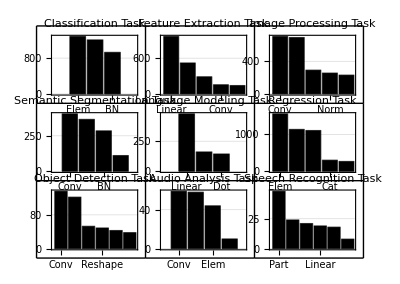

```mathematica
GraphicsGrid[Partition[figs,UpTo[3]],Frame->All,ImageMargins->0, ImageSize->Scaled[0.75]]
```

```mathematica
Import["http://tinyurl.com/ntmhkca"]
```

```mathematica
layers
```

<|ConvolutionLayer→1207,BatchNormalizationLayer→929,ElementwiseLayer→1284|>

```mathematica
tasks=Union[Flatten[Map[NetModel[ #,"TaskType"]&,Keys[$Models]]]]
```

{Audio Analysis,Classification,Feature Extraction,Image Processing,Language Modeling,Object Detection,Regression,Semantic Segmentation,Speech Recognition}

```mathematica
task="Object Detection";
ms=Lookup[$Models,models[task]];
layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];
ms=Association[Table[model->With[{info=Counts[Flatten[$Models[model]][[All,0,1]]]},Table[Lookup[info,layer,0],{layer,Keys[layers]}]],{model,models[task]}]];
```

```mathematica
Keys[models]
```

{Speech Recognition,Audio Analysis,Object Detection,Regression,Language Modeling,Semantic Segmentation,Image Processing,Feature Extraction,Classification}

```mathematica
Keys[layers]
```

{ElementwiseLayer,LinearLayer,DotLayer,ConvolutionLayer,BatchNormalizationLayer}

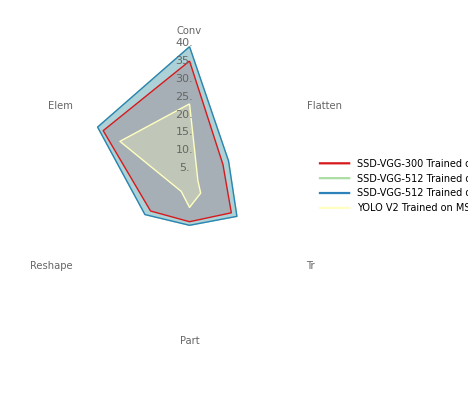

```mathematica
Needs["RadarChart`"]
RadarChart[Values[ms],Filling->Axis,AxesLabel->Map[Style[StringReplace[SymbolName[#],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}],FontSize->10,FontFamily->"Latin Modern Roman"]&,Keys[layers]],PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1]},ChartLegends->Keys[ms]]
```

## Model Layer Distribution

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

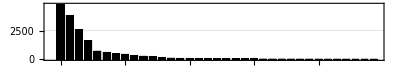

```mathematica
data=ReverseSort[Counts[Flatten[Values[$Models]][[All,0,1]]]];
BarChart[
data,
ChartLabels->Map[Rotate[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

## Model Uniqueness

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

```mathematica
unq=Association@KeyValueMap[
Function[{key,val},
key->{Length[val],Length[Union[val]],N[Length[Union[val]]/Length[val]]}
],
$Models
];
```

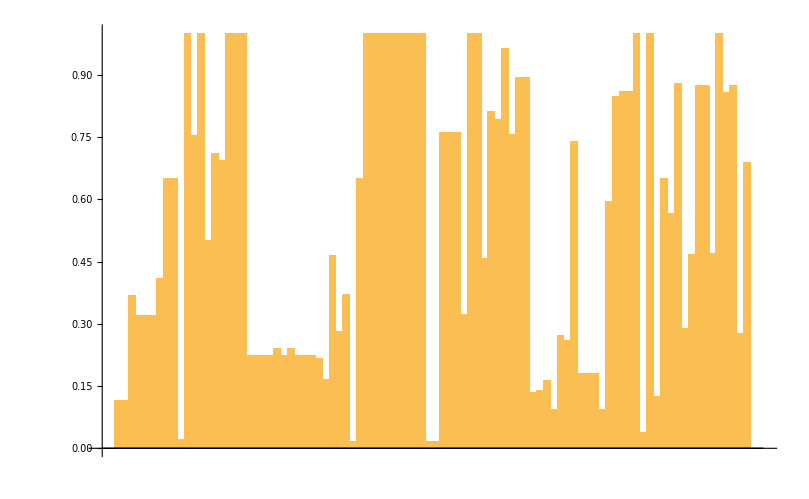

```mathematica
BarChart[MapThread[Tooltip,{Values[unq][[All,-1]],Keys[unq]}],PlotRange->All]
```

```mathematica
Grid[Normal[Select[unq,#[[-1]]<0.5&]]/.HoldPattern[Rule[x__]]:>Flatten[List[x]],Frame->All]
```

2D Face Alignment Net Trained on 300W Large Pose Data | 967 | 112 | 0.115822
3D Face Alignment Net Trained on 300W Large Pose Data | 967 | 112 | 0.115822
AdaIN-Style Trained on MS-COCO and Painter by Numbers Data | 109 | 40 | 0.366972
Ademxapp Model A1 Trained on ADE20K Data | 141 | 45 | 0.319149
Ademxapp Model A1 Trained on Cityscapes Data | 141 | 45 | 0.319149
Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data | 141 | 45 | 0.319149
Ademxapp Model A Trained on ImageNet Competition Data | 142 | 58 | 0.408451
BERT Trained on BookCorpus and English Wikipedia Data | 862 | 19 | 0.0220418
CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Monet-to-Photo Translation | 94 | 21 | 0.223404
CycleGAN Orange-to-Apple Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Photo-to-Cezanne Translation | 96 | 23 | 0.239583
CycleGAN Photo-to-Monet Translation | 94 | 21 | 0.223404
CycleGAN Photo-to-Van Gogh Translation | 96 | 23 | 0.239583
CycleGAN Summer-to-Winter Translation | 94 | 21 | 0.223404
CycleGAN Winter-to-Summer Translation | 94 | 21 | 0.223404
CycleGAN Zebra-to-Horse Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
Deep Speech 2 Trained on Baidu English Data | 152 | 33 | 0.217105
Dilated ResNet-105 Trained on Cityscapes Data | 360 | 60 | 0.166667
Dilated ResNet-22 Trained on Cityscapes Data | 86 | 40 | 0.465116
Dilated ResNet-38 Trained on Cityscapes Data | 142 | 40 | 0.28169
ELMo Contextual Word Representations Trained on 1B Word Benchmark | 111 | 41 | 0.369369
Enhanced Super-Resolution GAN Trained on DIV2K, Flickr2K and OST Data | 1093 | 17 | 0.0155535
GPT-2 Transformer Trained on WebText Data | 832 | 14 | 0.0168269
GPT Transformer Trained on BookCorpus Data | 857 | 15 | 0.0175029
Inception V3 Trained on ImageNet Competition Data | 311 | 100 | 0.321543
MobileNet V2 Trained on ImageNet Competition Data | 153 | 70 | 0.457516
ResNet-101 Trained on Augmented CASIA-WebFace Data | 345 | 46 | 0.133333
ResNet-101 Trained on ImageNet Competition Data | 347 | 48 | 0.138329
ResNet-101 Trained on YFCC100m Geotagged Data | 344 | 56 | 0.162791
ResNet-152 Trained on ImageNet Competition Data | 517 | 48 | 0.0928433
ResNet-50 Trained on ImageNet Competition Data | 177 | 48 | 0.271186
Self-Normalizing Net for Numeric Data | 23 | 6 | 0.26087
Single-Image Depth Perception Net Trained on Depth in the Wild Data | 501 | 90 | 0.179641
Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data | 501 | 90 | 0.179641
Single-Image Depth Perception Net Trained on NYU Depth V2 Data | 501 | 90 | 0.179641
Squeeze-and-Excitation Net Trained on ImageNet Competition Data | 874 | 82 | 0.0938215
Unguided Volumetric Regression Net for 3D Face Reconstruction | 1029 | 40 | 0.0388727
Very Deep Net for Super-Resolution | 40 | 5 | 0.125
Wide ResNet-50-2 Trained on ImageNet Competition Data | 176 | 51 | 0.289773
Wolfram AudioIdentify V1 Trained on AudioSet Data | 156 | 73 | 0.467949
Wolfram ImageIdentify Net V1 | 232 | 109 | 0.469828
Yahoo Open NSFW Model V1 | 177 | 49 | 0.276836

```mathematica
Length[Union[$Models["MobileNet V2 Trained on ImageNet Competition Data"]]]/N@Length[$Models["MobileNet V2 Trained on ImageNet Competition Data"]]
```

0.457516

## Model Sharing across networks

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
$ModelNames=Keys[$Models];
MapIndexed[Rule,Keys[$Models]];
```

```mathematica
resnet50=$Models[[65]];
resnet50Name="ResNet-50 Trained on ImageNet Competition Data";
inceptionv3=$Models[[51]];
inceptionv3Name="Inception V3 Trained on ImageNet Competition Data";
```

```mathematica
Length[Union[resnet50]]+Length[Union[inceptionv3]]
```

148

```mathematica
Length[Union[Flatten[{resnet50,inceptionv3}]]]
```

147

```mathematica
Keys[models]
```

{Speech Recognition,Other,Audio Analysis,Object Detection,Regression,Language Modeling,Semantic Segmentation,Image Processing,Feature Extraction,Classification}

```mathematica
taskType="Classification";
taskType="Object Detection";
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
data=Table[
k1=tuples[[1]];
k2=tuples[[2]];
m1=$Models[k1];
m2=$Models[k2];
Length[DeleteDuplicates[Flatten[{m1,m2}]]]/(Length[DeleteDuplicates[m1]]+Length[DeleteDuplicates[m2]]),
{tuples,Tuples[models[taskType],{2}]}
];
```

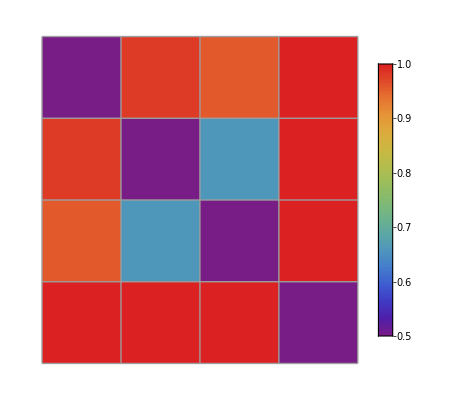

```mathematica
ArrayPlot[Partition[data,Length[models[taskType]]],ColorFunction->"Rainbow",Mesh->True,PlotLegends->Automatic,ImageSize->Scaled[0.5]]
```

```mathematica
ArrayPlot[Partition[data,Length[models[taskType]]],Mesh->True,Frame->True,PlotLegends->Automatic,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->All]
```

-Graphics-

### ignoring input and output shape

```mathematica
removeInputOutputSize[lyr_[assoc_,r___]]:=lyr[Append[assoc,"Parameters"->KeyDrop[assoc["Parameters"],{"$SpatialDimensions","$InputChannels","$InputSize","$OutputSize"}]]]
```

```mathematica
data=Table[
k1=tuples[[1]];
k2=tuples[[2]];
m1=removeInputOutputSize/@$Models[k1];
m2=removeInputOutputSize/@$Models[k2];
Length[DeleteDuplicates[Flatten[{m1,m2}]]]/(Length[DeleteDuplicates[m1]]+Length[DeleteDuplicates[m2]]),
{tuples,Tuples[models["Classification"],{2}]}
];
```

```mathematica
m1[[;;2]]
```

{ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{3,224,224},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→64,KernelSize→{7,7},Stride→{2,2},PaddingSize→{{3,3},{3,3}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→3|>|>],BatchNormalizationLayer[<|Type→BatchNormalization,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Parameters→<|Momentum→0.9,Epsilon→0.0001,$Channels→64,Interleaving→False|>|>]}

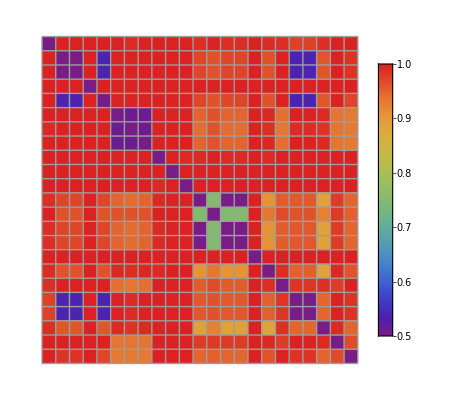

```mathematica
ArrayPlot[Partition[data,Length[models["Classification"]]],ColorFunction->"Rainbow",Mesh->True,PlotLegends->Automatic,ImageSize->Scaled[0.5]]
```

```mathematica
$Models[models["Classification"][[;;2]]]
```

Missing[KeyAbsent,{Ademxapp Model A Trained on ImageNet Competition Data,Age Estimation VGG-16 Trained on IMDB-WIKI and Looking at People Data}]

```mathematica
Column[removeInputOutputSize/@Select[RandomSample@Flatten[Lookup[$Models,models["Classification"][[;;3]]]],Head[#]===Inactive[ConvolutionLayer]&][[;;5]]]
```

ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{64,112,112},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{128,112,112},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→128,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→64|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{512,28,28},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{512,28,28},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→512,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→512|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{64,160,160},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{128,160,160},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→128,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→64|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{256,56,56},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{256,56,56},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→256,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→256|>|>]
ConvolutionLayer[<|Type→Convolution,Arrays→Null,Inputs→<|Input→NeuralNetworks`TensorT[{128,160,160},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{128,160,160},NeuralNetworks`RealT]|>,Parameters→<|OutputChannels→128,KernelSize→{3,3},Stride→{1,1},PaddingSize→{{1,1},{1,1}},Dilation→{1,1},Dimensionality→2,ChannelGroups→1,Interleaving→False,$WeightsInputChannels→128|>|>]

## Model Cache

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

## Generate Models MX File

```mathematica
Exit
```

```mathematica
PrependTo[$Path,NotebookDirectory[]];
```

```mathematica
<<SyntheticBenchmark`
<<SyntheticBenchmark`Assets`Models`
```

```mathematica
DumpSaveModelWeights[]
```

## Possible Names

Possible Names:
- PerSe
- Sybe
- ABUDL (* Analytic Benchmarking for Understanding DL *)
- DLSynBench
- SythBench
- Syn

## Scratch

### connected components

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
$ModelNames[[30]]
```

Deep Speech 2 Trained on Baidu English Data

```mathematica
model=NetModel[$ModelNames[[30]]];
```

```mathematica
NetInformation[model,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
NetInformation[model,"SummaryGraphic"]
```

-Graphics-

```mathematica
components=Select[
NetExtract[model,All],
MatchQ[#,_NetGraph]&
]
```

{}

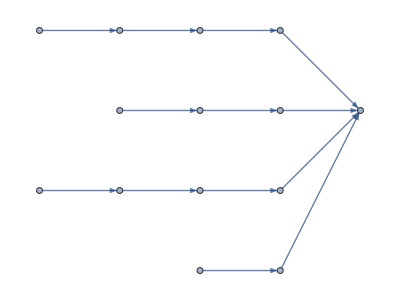

```mathematica
NetInformation[components[[1]],"LayersGraph"]
```

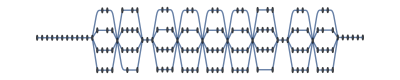

```mathematica
gr0=NetInformation[model,"LayersGraph"];
gr=Graph[VertexList[gr0],EdgeList[gr0]/.DirectedEdge->UndirectedEdge,Options[gr0]]
```

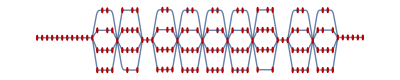

```mathematica
HighlightGraph[gr,ConnectedComponents[gr]]
```

### sequence

```mathematica
ClearAll[timeOf];
timeOf[{a->b,_}]:=ab;
timeOf[{b->c,_}]:=bc;
timeOf[{b->e,e->x_}]:=timeOf[{b->x,dummy}];
timeOf[{e->x_,_}]:=0;
timeOf[{c->d,_}]:=cd;
timeOf[{b->d,_}]:=bd;
```

```mathematica
ClearAll[transform];
transform[b->x_]:=If[RandomInteger[5]>2,{b->e,e->x},b->x];
transform[x_]:=x;
```

```mathematica
net0={a->b,b->c,c->d};
net1={a->b,b->d,c->d};
net2={a->b,b->d};
```

```mathematica
publicNet=Flatten[Map[transform,{net0,net1,net2},{2}]]
```

{a→b,b→c,c→d,a→b,b→e,e→d,c→d,a→b,b→e,e→d}

```mathematica
publicNet=Partition[Append[publicNet,dummy],2,1];
```

```mathematica
publicTimes=Association[Table[First[k]->timeOf[k],{k,publicNet}]]
```

<|(a→b)→ab,(b→c)→bc,(c→d)→cd,(b→e)→bd,(e→d)→0|>

```mathematica
Lookup[publicTimes,net0]
```

{ab,bc,cd}

```mathematica
Lookup[publicTimes,net1]
```

{ab,Missing[KeyAbsent,b→d],cd}

### Benchmarking

```mathematica
<<NeuralNetworks`
```

```mathematica
PrependTo[$ContextPath,"NeuralNetworks`Private`Benchmarking`"];
```

```mathematica
synthesizeData=NeuralNetworks`Private`Benchmarking`synthesizeData;
Inputs=NeuralNetworks`Private`Inputs;
NetAttachLoss=NeuralNetworks`NetAttachLoss;
```

```mathematica
batches=1;
batchSize=16;
NeuralNetworks`Private`Benchmarking`dataSize=batches*batchSize;
sequenceLength=32;
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
$ModelNames=Keys[$Models];
```

```mathematica
modelName="ResNet-50 Trained on ImageNet Competition Data";
```

```mathematica
model=NetModel[modelName];
lyrs=NetInformation[model,"Layers"];
```

```mathematica
Values[lyrs[min;;max]]
```

Values::invrl: The argument Missing[KeyAbsent,3;;4] is not a valid Association or a list of rules.

Values[Missing[KeyAbsent,3;;4]]

```mathematica
min=3;
max=3;
lyr=lyrs[[min]];
net=NetChain[Values[lyrs][[min;;max]]];
tnet=NetInitialize@NetAttachLoss[net,Automatic];
SeedRandom[1];
tdata=synthesizeData/@Inputs[lyr];
Min[Table[First[AbsoluteTiming[net[tdata];]],10]]
```

0.187678

```mathematica
net
```

NetChain[<>]

```mathematica
timings=Association@Table[
max=min;
lyr=lyrs[[min]];
net=NetChain[Values[lyrs][[min;;max]]];
tnet=NetInitialize@NetAttachLoss[net,Automatic];
SeedRandom[1];
tdata=synthesizeData/@Inputs[lyr];
min->Min[Table[First[AbsoluteTiming[net[tdata];]],2]],
{min,Length[lyrs[[;;20]]]}
]
```

<|1→0.277206,2→0.229379,3→0.212302,4→0.263796,5→0.15866,6→0.257963,7→0.227629,8→0.083847,9→0.053205,10→0.059507,11→0.14178,12→0.048539,13→0.057621,14→0.216504,15→0.2329,16→0.240297,17→0.20192,18→0.124089,19→0.063094,20→0.058192|>

```mathematica
NetInformation[lyrs[[2]],"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
NetInformation[model,"SummaryGraphic"]
```

-Graphics-

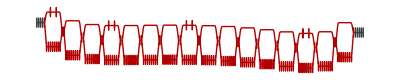

```mathematica
gr=UndirectedGraph[ NetInformation[model,"LayersGraph"]];
cycles=FindCycle[gr,Infinity,All];
Fold[HighlightGraph[#1,PathGraph[#2]]&,gr,cycles]
```

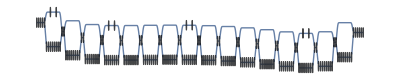

```mathematica
gr
```

```mathematica
NetInformation[lyrs[[2]],"InputPorts"]
```

<|Input→{64,112,112}|>

```mathematica
lyrs[[2]]
```

BatchNormalizationLayer[<>]

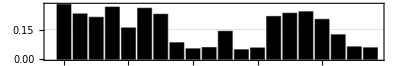

```mathematica
BarChart[
timings,
ChartLabels->Map[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"]&,Keys[timings]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

### Hatching

```mathematica
inPolyQ=Compile[{{polygon,_Real,2},{x,_Real},{y,_Real}},Block[{polySides=Length[polygon],X=polygon[[All,1]],Y=polygon[[All,2]],Xi,Yi,Yip1,wn=0,i=1},While[i<polySides,Yi=Y[[i]];Yip1=Y[[i+1]];
If[Yi≤y,If[Yip1>y,Xi=X[[i]];
If[(X[[i+1]]-Xi) (y-Yi)-(x-Xi) (Yip1-Yi)>0,wn++;];];,If[Yip1≤y,Xi=X[[i]];
If[(X[[i+1]]-Xi) (y-Yi)-(x-Xi) (Yip1-Yi)<0,wn--;];];];i++];!wn==0]];
```

```mathematica
poly=Rescale[ExampleData[{"Statistics","WesternUgandaBorder"}]];
```

CompiledFunction::cfsa: Argument x at position 2 should be a machine-size real number.

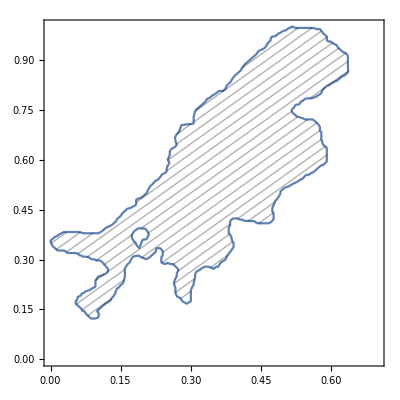

```mathematica
RegionPlot[inPolyQ[poly,x,y],{x,0,.7},{y,0,1},Mesh->20,MeshFunctions->{#1-#2&},MeshShading->{None},PlotPoints->25]
```